# Introduction to Mathematica

## #CA1 #Q3 Signals & Systems Mohammad GharehHasanloo

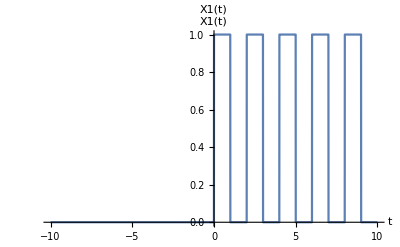

```mathematica
X1[t_]:=∑_(n=0)^Infinity (UnitStep[t-2n])*(UnitStep[1+2*n-t])
Plot[ X1[t], {t, -10, 10},PlotLabel->"X1(t)",AxesLabel->{"t","X1(t)"}]
```

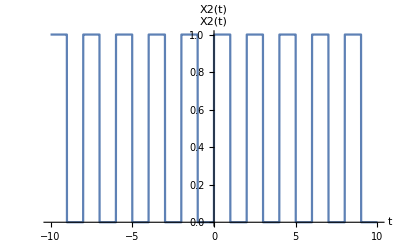

```mathematica
X2[t_]:=∑_(n=-Infinity)^Infinity (UnitStep[t-2n])*(UnitStep[1+2*n-t])
Plot[ X2[t], {t, -10, 10},PlotLabel->"X2(t)",AxesLabel->{"t","X2(t)"}]
```

```mathematica
X3[t_]:=Cos[2*t] + Sin[3*t]
Manipulate[Plot[{X3[t+T], X3[t]}, {t, -10, 10},PlotLabel->"X3(t)",AxesLabel->{"t","X3(t)"}],{T,0,20}]
```

```mathematica
X4[t_]:=Cos[(Pi*t)/5] + Sin[(Pi*t)/3]
Manipulate[Plot[{X4[t+T], X4[t]}, {t, -20, 20},PlotLabel->"X4(t)",AxesLabel->{"t","X4(t)"}],{T,0,60}]
```

```mathematica
X5[t_]:=Sin[t]*UnitStep[t]
Manipulate[Plot[{(X5[t+T]+X5[-(t+T)])/2, (X5[t]+X5[-t])/2}, {t, -20, 20},PlotLabel->"X5(t)",AxesLabel->{"t","X5(t)"}],{T,0,100}]
```

```mathematica
X6[t_]:=Cos[t]*UnitStep[t]
Manipulate[Plot[{(X6[t+T]+X6[-(t+T)])/2, (X6[t]+X6[-t])/2}, {t, -20, 20},PlotLabel->"X6(t)",AxesLabel->{"t","X6(t)"}],{T,0,100}]
```

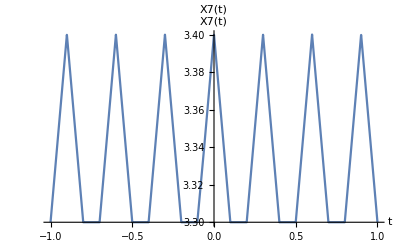

```mathematica
X7[t_]:=∑_(k=-100)^100 (Ramp[(t-0.3*k)+1]-2Ramp[t-0.3*k]+Ramp[(t-0.3*k)-1])
Plot[ X7[t], {t, -1, 1},PlotLabel->"X7(t)",AxesLabel->{"t","X7(t)"}]
```